## O_h irreps and decompositions

```mathematica
OhRed=<|
"Irreps"->{"A_(1  g)","A_(2  g)","E_g","T_(1  g)","T_(2  g)"},
"CharacterTable"->
{
{1,1,1,1,1},
{1,1,-1,-1,1},
{2,-1,0,0,2},
{3,0,-1,1,-1},
{3,0,1,-1,-1}
},
"ConjugacyClassSizes"->{1,8,6,6,3}
|>;
```

```mathematica
Oh=<|
"Irreps"->{"A_(1  g)","A_(2  g)","E_g","T_(1  g)","T_(2  g)","A_(1  u)","A_(2  u)","E_u","T_(1  u)","T_(2  u)"},
"CharacterTable"->
Flatten[KroneckerProduct[
({{1, 1}, {1, -1}}),
{
{1,1,1,1,1},
{1,1,-1,-1,1},
{2,-1,0,0,2},
{3,0,-1,1,-1},
{3,0,1,-1,-1}
}],{1}],
"ConjugacyClassSizes"->{1,8,6,6,3,1,8,6,6,3}
|>;
```

```mathematica
IsotypicDecomposition[G_Association,char__]:=Module[{multi},
multi=Table[1/Total[G["ConjugacyClassSizes"]](G["ConjugacyClassSizes"]G["CharacterTable"][[i]]).char,{i,Length[G["CharacterTable"]]}];

multi=DeleteCases[multi G["Irreps"],0];

If[Length[multi]>1,multi/.List->CirclePlus,multi[[1]]]
]
```

```mathematica
χO3[l_,θ_]:=ChebyshevU[2l,Cos[θ/2]](*:=Sin[(l+1/2)θ]/Sin[1/2 θ]*)
χO3Red[l_]:=χO3[l,#]&/@{0,2π/3,π,π/2,π}
χO3Full[l_]:=Flatten[KroneckerProduct[{1,(-1)^l},χO3Red[l]],1]
χ[name_,G_:Oh]:=G["CharacterTable"][[Position[G["Irreps"],name][[1,1]]]]
```

```mathematica
l=1;
χO3Red[l]
χO3Full[l]
IsotypicDecomposition[Oh,χO3Full[l]]
```

{3,0,-1,1,-1}

{3,0,-1,1,-1,-3,0,1,-1,1}

T_(1  u)

```mathematica
l=2;
χO3Red[l]
χO3Full[l]
IsotypicDecomposition[Oh,χO3Full[l]]
```

{5,-1,1,-1,1}

{5,-1,1,-1,1,5,-1,1,-1,1}

E_g⊕T_(2  g)

```mathematica
l=3;
χO3Red[l]
χO3Full[l]
IsotypicDecomposition[Oh,χO3Full[l]]
```

{7,1,-1,-1,-1}

{7,1,-1,-1,-1,-7,-1,1,1,1}

A_(2  u)⊕T_(1  u)⊕T_(2  u)

```mathematica
l=4;
χO3Red[l]
χO3Full[l]
IsotypicDecomposition[Oh,χO3Full[l]]
```

{9,0,1,1,1}

{9,0,1,1,1,9,0,1,1,1}

A_(1  g)⊕E_g⊕T_(1  g)⊕T_(2  g)

## Superconductivity Order Parameter

```mathematica
D4=<|
"Irreps"->{"A_1","A_2","B_1","B_2","E"},
"CharacterTable"->
{
{1,1,1,1,1},
{1,1,1,-1,-1},
{1,-1,1,1,-1},
{1,-1,1,-1,1},
{2,0,-2,0,0}
},
"ConjugacyClasses"->{"E","C_4","C_2^z","C'_2","C''_2"},
"ConjugacyClassSizes"->{1,2,1,2,2}
|>;
```

```mathematica
(*Matrix rep in the basis {e^Subscript[ik, x],e^Subscript[ik, y],e^(-Subscript[ik, x]),e^(-Subscript[ik, y])}*)
NNBasis={ⅇ^(ⅈ Subscript[k, x]),ⅇ^(ⅈ Subscript[k, y]),ⅇ^(-ⅈ Subscript[k, x]),ⅇ^(-ⅈ Subscript[k, y])};
D4gens={
(*Subscript[C, 4]*)({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}}),
(*Subscript[σ, x]=Subscript[C, 2]'*)({{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}})
};
MatrixForm/@(D4mats=Flatten[Table[MatrixPower[D4gens[[1]],i].MatrixPower[D4gens[[2]],j],{i,0,3},{j,0,1}],1])
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
D4matClasses={"E","C'_2","C_4","C''_2","C_2^z","C'_2","C_4","C''_2"};
```

```mathematica
projectorD4[irrep_]:=Module[{repind},
repind=Position[D4["Irreps"],irrep][[1,1]];
(D4["CharacterTable"][[repind,1]])/8∑_(i=1)^8 D4["CharacterTable"][[repind,Position[D4["ConjugacyClasses"],D4matClasses[[i]]][[1,1]]]]D4mats[[i]]
]
```

```mathematica
projectors={PA1,PA2,PB1,PB2,PE}=projectorD4/@D4["Irreps"];
```

```mathematica
TableForm[{MatrixForm/@projectors},TableHeadings->{None,D4["Irreps"]}]
```

A_1 | A_2 | B_1 | B_2 | E
(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | 1/4 | 1/4) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4
1/4 | -1/4 | 1/4 | -1/4
-1/4 | 1/4 | -1/4 | 1/4) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/2 | 0 | -1/2 | 0
0 | 1/2 | 0 | -1/2
-1/2 | 0 | 1/2 | 0
0 | -1/2 | 0 | 1/2)

```mathematica
#.#==#&/@projectors
```

{True,True,True,True,True}

```mathematica
Eigensystem[PA1]
```

{{1,0,0,0},{{1,1,1,1},{-1,0,0,1},{-1,0,1,0},{-1,1,0,0}}}

```mathematica
Normalize[{1,1,1,1}].NNBasis//ExpToTrig
```

Cos[k_x]+Cos[k_y]

```mathematica
Eigensystem[PB1]
```

{{1,0,0,0},{{-1,1,-1,1},{1,0,0,1},{-1,0,1,0},{1,1,0,0}}}

```mathematica
Normalize[-{-1,1,-1,1}].NNBasis//ExpToTrig
```

Cos[k_x]-Cos[k_y]

```mathematica
Eigensystem[PE]
```

{{1,1,0,0},{{0,-1,0,1},{-1,0,1,0},{0,1,0,1},{1,0,1,0}}}

```mathematica
Normalize[{0,-1,0,1}].NNBasis//ExpToTrig
Normalize[{-1,0,1,0}].NNBasis//ExpToTrig
```

-ⅈ √2 Sin[k_y]

-ⅈ √2 Sin[k_x]

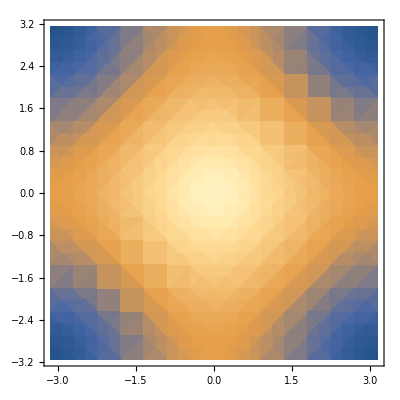

```mathematica
DensityPlot[Cos[kx]+Cos[ky],{kx,-π,π},{ky,-π,π},MeshFunctions->{#3&,#3&},Mesh->{{0},{0}},MeshStyle->Opacity[0.5,Black]]
```

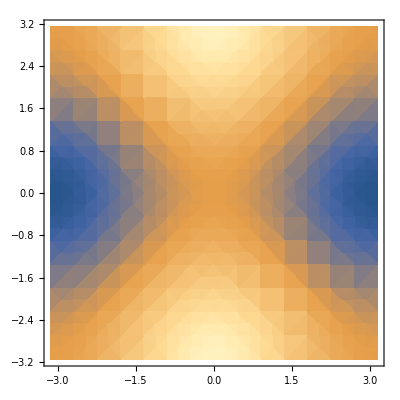

```mathematica
DensityPlot[Cos[kx]-Cos[ky],{kx,-π,π},{ky,-π,π},MeshFunctions->{#3&,#3&},Mesh->{{0},{0}},MeshStyle->Opacity[0.5,Black]]
```

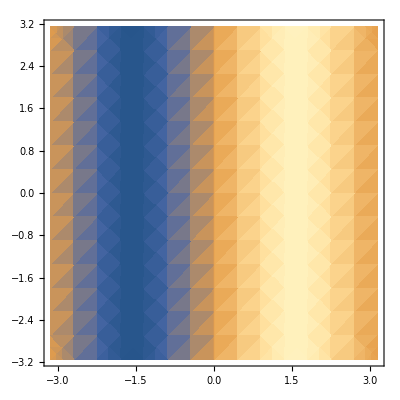

```mathematica
DensityPlot[Sin[kx],{kx,-π,π},{ky,-π,π},MeshFunctions->{#3&,#3&},Mesh->{{0},{0}},MeshStyle->Opacity[0.5,Black]]
```

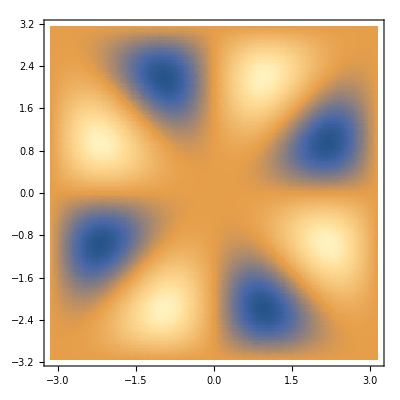

```mathematica
DensityPlot[Sin[kx]Sin[ky](Cos[kx]-Cos[ky]),{kx,-π,π},{ky,-π,π},MeshFunctions->{#3&,#3&},Mesh->{{0},{0}},MeshStyle->Opacity[0.5,Black],PlotPoints->150]
```